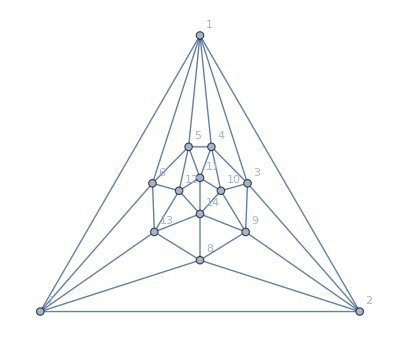

```mathematica
pl1=Graph[plantri[[2]],VertexLabels->"Name", GraphLayout->"TutteEmbedding"]
```

```mathematica
ffpl1=FindFullFormula[pl1];
```

```mathematica
pl1gen=Select[ffpl1,StringCount[SymbolName[#],"x"]==3&]
```

{v1ex25adx368bx479c,v1adx25ex368bx479c,v19bdx2acx357ex468,v19bdx26ax357ex48c,v19cx25adx368bx47e,v19bdx246ex38cx57a,v19bdx246ex37cx58a,v19bdx246x357ex8ac,v19bdx246ex357x8ac,v19bdx246ex358x7ac,v19bdx24cx357ex68a,v18acx2bdx357ex469,v18acx26bx357ex49d,v18bx25adx36ex479c,v18acx246ex3bdx579,v18acx246ex37bx59d,v18acx246x357ex9bd,v18acx246ex357x9bd,v18acx246ex35dx79b,v18acx24dx357ex69b}

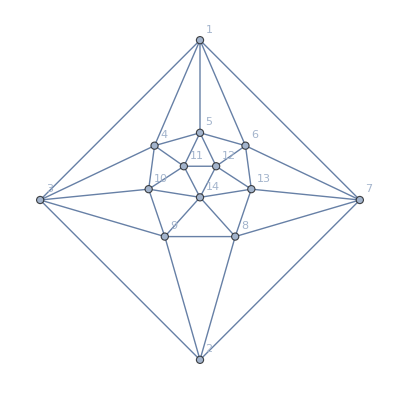

```mathematica
pl2=EdgeDelete[pl1,1<->2]
```

```mathematica
ChromaticPolynomial[pl1,7]
```

1331914920

```mathematica
Table[ChromaticPolynomial[pl1,k]/k!,{k,4,12}]
```

{20,3465,56925,1585613/6,541073,4965335/8,33119939/72,81152371/336,45942707/480}

```mathematica
ffpl2=FindFullFormula[pl2];
```

```mathematica
pl2gen=Select[ffpl2,StringCount[SymbolName[#],"x"]==3&]
```

{v1ex25adx368bx479c,v1adx25ex368bx479c,v19bdx2acx357ex468,v19bdx26ax357ex48c,v19cx25adx368bx47e,v19bdx246ex38cx57a,v19bdx246ex37cx58a,v19bdx246x357ex8ac,v19bdx246ex357x8ac,v19bdx246ex358x7ac,v19bdx24cx357ex68a,v18acx2bdx357ex469,v18acx26bx357ex49d,v18bx25adx36ex479c,v18acx246ex3bdx579,v18acx246ex37bx59d,v18acx246x357ex9bd,v18acx246ex357x9bd,v18acx246ex35dx79b,v18acx24dx357ex69b,v12adx368bx49cx57e,v12acx368bx49dx57e,v12adx368bx479cx5e,v12ex368bx479cx5ad,v12acx368bx47ex59d,v12bdx36ex479cx58a,v12bdx357ex49cx68a,v12adx357ex49cx68b,v12acx357ex49dx68b,v12adx357ex48cx69b,v12bdx35ex479cx68a,v12adx35ex479cx68b,v12acx357ex468x9bd,v12bdx357ex469x8ac}

```mathematica
Tally[Map[StringCount[SymbolName[#],"x"]&,ffpl1]]//Sort
```

{{3,20},{4,3445},{5,53470},{6,209073},{7,304690},{8,202385},{9,68167},{10,12222},{11,1165},{12,55},{13,1}}

```mathematica
Tally[Map[StringCount[SymbolName[#],"x"]&,ffpl3]]//Sort
```

{{3,8},{4,299},{5,1448},{6,2074},{7,1145},{8,273},{9,28},{10,1}}

```mathematica
Tally[Map[StringCount[SymbolName[#],"x"]&,ffpl2]]//Sort
```

{{3,34},{4,4858},{5,69557},{6,255498},{7,355199},{8,227348},{9,74285},{10,12981},{11,1210},{12,56},{13,1}}

```mathematica
(Most[Tally[Map[StringCount[SymbolName[#],"x"]&,ffpl1]]//Sort])+(Tally[Map[StringCount[SymbolName[#],"x"]&,ffpl3]]//Sort)
```

Thread::tdlen: Objects of unequal length in {{3,20},{4,3445},{5,53470},{6,209073},{7,304690},{8,202385},{9,68167},{10,12222},{11,1165},{12,55}}+{{3,8},{4,299},{5,1448},{6,2074},{7,1145},{8,273},{9,28},{10,1}} cannot be combined.

{{3,8},{4,299},{5,1448},{6,2074},{7,1145},{8,273},{9,28},{10,1}}+{{3,20},{4,3445},{5,53470},{6,209073},{7,304690},{8,202385},{9,68167},{10,12222},{11,1165},{12,55}}

```mathematica
EdgeList[pl1]//Sort
```

{1<->2,1<->3,1<->4,1<->5,1<->6,1<->7,2<->3,2<->7,2<->8,2<->9,3<->4,3<->9,3<->10,4<->5,4<->10,4<->11,5<->6,5<->11,5<->12,6<->7,6<->12,6<->13,7<->8,7<->13,8<->9,8<->13,8<->14,9<->10,9<->14,10<->11,10<->14,11<->12,11<->14,12<->13,12<->14,13<->14}

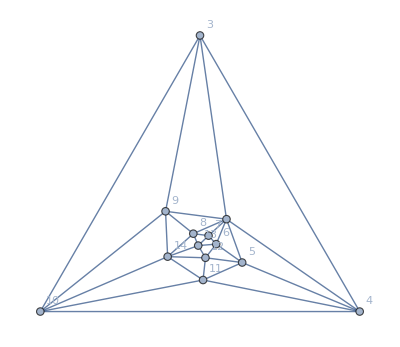

```mathematica
pl3=EdgeContract[pl1,1<->2]
```

```mathematica
EdgeList[pl3]
```

{3<->9,3<->10,3<->4,4<->10,4<->11,4<->5,5<->11,5<->12,5<->6,6<->12,6<->13,6<->7,7<->13,7<->8,8<->13,8<->14,8<->9,9<->14,9<->10,10<->14,10<->11,11<->14,11<->12,12<->14,12<->13,13<->14,1<->3,1<->4,1<->5,1<->6,1<->7,1<->8,1<->9}

```mathematica
ffpl3=FindFullFormula[pl3];
```

```mathematica
Add2[sets_]:=Block[{},SortSets[Table[If[MemberQ[s,1],Sort[Append[s,2]],s],{s,sets}]]]
```

```mathematica
preselect=Select[ffpl3,StringCount[SymbolName[#],"x"]==3&]
```

{v1adx368bx49cx57e,v1acx368bx49dx57e,v1adx368bx479cx5e,v1ex368bx479cx5ad,v1acx368bx47ex59d,v1bdx36ex479cx58a,v1bdx357ex49cx68a,v1adx357ex49cx68b,v1acx357ex49dx68b,v1adx357ex48cx69b,v1bdx35ex479cx68a,v1adx35ex479cx68b,v1acx357ex468x9bd,v1bdx357ex469x8ac}

```mathematica
pl3gen=Sort[Table[SetsToSymbol2[SortSets[Add2[SymbolToSets[k]]]],{k,preselect}]]
```

{v12acx357ex468x9bd,v12acx357ex49dx68b,v12acx368bx47ex59d,v12acx368bx49dx57e,v12adx357ex48cx69b,v12adx357ex49cx68b,v12adx35ex479cx68b,v12adx368bx479cx5e,v12adx368bx49cx57e,v12bdx357ex469x8ac,v12bdx357ex49cx68a,v12bdx35ex479cx68a,v12bdx36ex479cx58a,v12ex368bx479cx5ad}

```mathematica
Remove12[sets_]:=SortSets[Map[Select[#,!MemberQ[{1,2},#]&]&,sets]]
```

## one by one

```mathematica
pl1gen
```

{v1ex25adx368bx479c,v1adx25ex368bx479c,v19bdx2acx357ex468,v19bdx26ax357ex48c,v19cx25adx368bx47e,v19bdx246ex38cx57a,v19bdx246ex37cx58a,v19bdx246x357ex8ac,v19bdx246ex357x8ac,v19bdx246ex358x7ac,v19bdx24cx357ex68a,v18acx2bdx357ex469,v18acx26bx357ex49d,v18bx25adx36ex479c,v18acx246ex3bdx579,v18acx246ex37bx59d,v18acx246x357ex9bd,v18acx246ex357x9bd,v18acx246ex35dx79b,v18acx24dx357ex69b}

```mathematica
pl1genbis=Map[SetsToSymbol2[#]&,Sort[Map[Remove12[#]&,Map[SymbolToSets[#]&,pl1gen]]]]
```

{v357x46ex8acx9bd,v357x46ex8acx9bd,v358x46ex7acx9bd,v35dx46ex79bx8ac,v36ex479cx5adx8b,v37bx46ex59dx8ac,v37cx46ex58ax9bd,v38cx46ex57ax9bd,v3bdx46ex579x8ac,v357ex46x8acx9bd,v357ex46x8acx9bd,v357ex4cx68ax9bd,v357ex4dx69bx8ac,v357ex468x9bdxac,v357ex469x8acxbd,v357ex48cx6ax9bd,v357ex49dx6bx8ac,v368bx47ex5adx9c,v368bx479cx5exad,v368bx479cx5adxe}

```mathematica
pl2gen
```

{v1ex25adx368bx479c,v1adx25ex368bx479c,v19bdx2acx357ex468,v19bdx26ax357ex48c,v19cx25adx368bx47e,v19bdx246ex38cx57a,v19bdx246ex37cx58a,v19bdx246x357ex8ac,v19bdx246ex357x8ac,v19bdx246ex358x7ac,v19bdx24cx357ex68a,v18acx2bdx357ex469,v18acx26bx357ex49d,v18bx25adx36ex479c,v18acx246ex3bdx579,v18acx246ex37bx59d,v18acx246x357ex9bd,v18acx246ex357x9bd,v18acx246ex35dx79b,v18acx24dx357ex69b,v12adx368bx49cx57e,v12acx368bx49dx57e,v12adx368bx479cx5e,v12ex368bx479cx5ad,v12acx368bx47ex59d,v12bdx36ex479cx58a,v12bdx357ex49cx68a,v12adx357ex49cx68b,v12acx357ex49dx68b,v12adx357ex48cx69b,v12bdx35ex479cx68a,v12adx35ex479cx68b,v12acx357ex468x9bd,v12bdx357ex469x8ac}

```mathematica
pl2genbis=Map[SetsToSymbol2[#]&,Sort[Map[Remove12[#]&,Map[SymbolToSets[#]&,pl2gen]]]]
```

{v357x46ex8acx9bd,v357x46ex8acx9bd,v358x46ex7acx9bd,v35dx46ex79bx8ac,v35ex479cx68axbd,v35ex479cx68bxad,v36ex479cx58axbd,v36ex479cx5adx8b,v37bx46ex59dx8ac,v37cx46ex58ax9bd,v38cx46ex57ax9bd,v3bdx46ex579x8ac,v357ex46x8acx9bd,v357ex46x8acx9bd,v357ex4cx68ax9bd,v357ex4dx69bx8ac,v357ex468x9bdxac,v357ex468x9bdxac,v357ex469x8acxbd,v357ex469x8acxbd,v357ex48cx6ax9bd,v357ex48cx69bxad,v357ex49cx68axbd,v357ex49cx68bxad,v357ex49dx6bx8ac,v357ex49dx68bxac,v368bx47ex59dxac,v368bx47ex5adx9c,v368bx49cx57exad,v368bx49dx57exac,v368bx479cx5exad,v368bx479cx5exad,v368bx479cx5adxe,v368bx479cx5adxe}

```mathematica
pl3gen
```

{v12acx357ex468x9bd,v12acx357ex49dx68b,v12acx368bx47ex59d,v12acx368bx49dx57e,v12adx357ex48cx69b,v12adx357ex49cx68b,v12adx35ex479cx68b,v12adx368bx479cx5e,v12adx368bx49cx57e,v12bdx357ex469x8ac,v12bdx357ex49cx68a,v12bdx35ex479cx68a,v12bdx36ex479cx58a,v12ex368bx479cx5ad}

```mathematica
pl3genbis=Map[SetsToSymbol2[#]&,Sort[Map[Remove12[#]&,Map[SymbolToSets[#]&,pl3gen]]]]
```

{v35ex479cx68axbd,v35ex479cx68bxad,v36ex479cx58axbd,v357ex468x9bdxac,v357ex469x8acxbd,v357ex48cx69bxad,v357ex49cx68axbd,v357ex49cx68bxad,v357ex49dx68bxac,v368bx47ex59dxac,v368bx49cx57exad,v368bx49dx57exac,v368bx479cx5exad,v368bx479cx5adxe}

```mathematica
rep1bis=Table[k->Style[k,Red],{k,Intersection[pl2genbis,pl1genbis]}]
```

{v357ex468x9bdxac→v357ex468x9bdxac,v357ex469x8acxbd→v357ex469x8acxbd,v357ex46x8acx9bd→v357ex46x8acx9bd,v357ex48cx6ax9bd→v357ex48cx6ax9bd,v357ex49dx6bx8ac→v357ex49dx6bx8ac,v357ex4cx68ax9bd→v357ex4cx68ax9bd,v357ex4dx69bx8ac→v357ex4dx69bx8ac,v357x46ex8acx9bd→v357x46ex8acx9bd,v358x46ex7acx9bd→v358x46ex7acx9bd,v35dx46ex79bx8ac→v35dx46ex79bx8ac,v368bx479cx5adxe→v368bx479cx5adxe,v368bx479cx5exad→v368bx479cx5exad,v368bx47ex5adx9c→v368bx47ex5adx9c,v36ex479cx5adx8b→v36ex479cx5adx8b,v37bx46ex59dx8ac→v37bx46ex59dx8ac,v37cx46ex58ax9bd→v37cx46ex58ax9bd,v38cx46ex57ax9bd→v38cx46ex57ax9bd,v3bdx46ex579x8ac→v3bdx46ex579x8ac}

```mathematica
rep3bis=Table[k->Style[k,Blue],{k,Intersection[pl2genbis,pl3genbis]}]
```

{v357ex468x9bdxac→v357ex468x9bdxac,v357ex469x8acxbd→v357ex469x8acxbd,v357ex48cx69bxad→v357ex48cx69bxad,v357ex49cx68axbd→v357ex49cx68axbd,v357ex49cx68bxad→v357ex49cx68bxad,v357ex49dx68bxac→v357ex49dx68bxac,v35ex479cx68axbd→v35ex479cx68axbd,v35ex479cx68bxad→v35ex479cx68bxad,v368bx479cx5adxe→v368bx479cx5adxe,v368bx479cx5exad→v368bx479cx5exad,v368bx47ex59dxac→v368bx47ex59dxac,v368bx49cx57exad→v368bx49cx57exad,v368bx49dx57exac→v368bx49dx57exac,v36ex479cx58axbd→v36ex479cx58axbd}

```mathematica
pl2genbis/.rep1bis/.rep3bis
```

{v357x46ex8acx9bd,v357x46ex8acx9bd,v358x46ex7acx9bd,v35dx46ex79bx8ac,v35ex479cx68axbd,v35ex479cx68bxad,v36ex479cx58axbd,v36ex479cx5adx8b,v37bx46ex59dx8ac,v37cx46ex58ax9bd,v38cx46ex57ax9bd,v3bdx46ex579x8ac,v357ex46x8acx9bd,v357ex46x8acx9bd,v357ex4cx68ax9bd,v357ex4dx69bx8ac,v357ex468x9bdxac,v357ex468x9bdxac,v357ex469x8acxbd,v357ex469x8acxbd,v357ex48cx6ax9bd,v357ex48cx69bxad,v357ex49cx68axbd,v357ex49cx68bxad,v357ex49dx6bx8ac,v357ex49dx68bxac,v368bx47ex59dxac,v368bx47ex5adx9c,v368bx49cx57exad,v368bx49dx57exac,v368bx479cx5exad,v368bx479cx5exad,v368bx479cx5adxe,v368bx479cx5adxe}

```mathematica
rep1=Table[k->Style[k,Darker[Green]],{k,Intersection[pl2gen,pl1gen]}]
```

{v18acx246ex357x9bd→v18acx246ex357x9bd,v18acx246ex35dx79b→v18acx246ex35dx79b,v18acx246ex37bx59d→v18acx246ex37bx59d,v18acx246ex3bdx579→v18acx246ex3bdx579,v18acx246x357ex9bd→v18acx246x357ex9bd,v18acx24dx357ex69b→v18acx24dx357ex69b,v18acx26bx357ex49d→v18acx26bx357ex49d,v18acx2bdx357ex469→v18acx2bdx357ex469,v18bx25adx36ex479c→v18bx25adx36ex479c,v19bdx246ex357x8ac→v19bdx246ex357x8ac,v19bdx246ex358x7ac→v19bdx246ex358x7ac,v19bdx246ex37cx58a→v19bdx246ex37cx58a,v19bdx246ex38cx57a→v19bdx246ex38cx57a,v19bdx246x357ex8ac→v19bdx246x357ex8ac,v19bdx24cx357ex68a→v19bdx24cx357ex68a,v19bdx26ax357ex48c→v19bdx26ax357ex48c,v19bdx2acx357ex468→v19bdx2acx357ex468,v19cx25adx368bx47e→v19cx25adx368bx47e,v1adx25ex368bx479c→v1adx25ex368bx479c,v1ex25adx368bx479c→v1ex25adx368bx479c}

```mathematica
rep3=Table[k->Style[k,Darker[Yellow]],{k,Intersection[pl2gen,pl3gen]}]
```

{v12acx357ex468x9bd→v12acx357ex468x9bd,v12acx357ex49dx68b→v12acx357ex49dx68b,v12acx368bx47ex59d→v12acx368bx47ex59d,v12acx368bx49dx57e→v12acx368bx49dx57e,v12adx357ex48cx69b→v12adx357ex48cx69b,v12adx357ex49cx68b→v12adx357ex49cx68b,v12adx35ex479cx68b→v12adx35ex479cx68b,v12adx368bx479cx5e→v12adx368bx479cx5e,v12adx368bx49cx57e→v12adx368bx49cx57e,v12bdx357ex469x8ac→v12bdx357ex469x8ac,v12bdx357ex49cx68a→v12bdx357ex49cx68a,v12bdx35ex479cx68a→v12bdx35ex479cx68a,v12bdx36ex479cx58a→v12bdx36ex479cx58a,v12ex368bx479cx5ad→v12ex368bx479cx5ad}

```mathematica
pl2gen/.rep1/.rep3
```

{v1ex25adx368bx479c,v1adx25ex368bx479c,v19bdx2acx357ex468,v19bdx26ax357ex48c,v19cx25adx368bx47e,v19bdx246ex38cx57a,v19bdx246ex37cx58a,v19bdx246x357ex8ac,v19bdx246ex357x8ac,v19bdx246ex358x7ac,v19bdx24cx357ex68a,v18acx2bdx357ex469,v18acx26bx357ex49d,v18bx25adx36ex479c,v18acx246ex3bdx579,v18acx246ex37bx59d,v18acx246x357ex9bd,v18acx246ex357x9bd,v18acx246ex35dx79b,v18acx24dx357ex69b,v12adx368bx49cx57e,v12acx368bx49dx57e,v12adx368bx479cx5e,v12ex368bx479cx5ad,v12acx368bx47ex59d,v12bdx36ex479cx58a,v12bdx357ex49cx68a,v12adx357ex49cx68b,v12acx357ex49dx68b,v12adx357ex48cx69b,v12bdx35ex479cx68a,v12adx35ex479cx68b,v12acx357ex468x9bd,v12bdx357ex469x8ac}

```mathematica
Map[Length,{pl1gen,pl2gen,pl3gen}]
```

{20,34,14}

```mathematica
Map[Length,{pl1genbis,pl2genbis,pl3genbis}]
```

{20,34,14}